```mathematica
(*1 - if left, -1 - if right , 0 - if on the line*)
PointLocation[{p1_,p2_},p3_]:= Block[{d},d= Det[{p2-p1,p3-p1}];
  If[d>0,Return [1],
If[d<0,Return[-1],Return[0]]]
];
```

```mathematica
(*метод определяющий взаимное расположение двух отрезков*)
IsIntersecting[{p1_,p2_},{p3_,p4_}] := Block[{d1,d2,d3,d4}, d1 = Det[{ p4-p3,p1-p3}]; d2 = Det[{p4-p3,p2-p3}]; d3 = Det[{p2-p1,p3-p1}]; d4 = Det[{p2-p1,p4-p1}];
s1=Dot[p3-p1,p4-p1];s2=Dot[p3-p2,p4-p2];s3=Dot[p3-p1,p3-p2];s4=Dot[p4-p1,p4-p2];
If[d1==d2==d3==d4==0 ,
	If[s1 ≤0 || s2 ≤0 || s3≤0 || s4 ≤0,Return[True],Return[False]]
	,If[(d1*d2 ≤ 0)&&(d3*d4≤0),Return[True],Return[False]]
]
];
```

```mathematica
GeneratePolygon[no_]:=Block[
{Po={{RandomInteger[{0,15}],RandomInteger[{0,15}]},{RandomInteger[{0,15}],RandomInteger[{0,15}]},{RandomInteger[{0,15}],RandomInteger[{0,15}]}},remain=True,intersect,cur,i,j},
While[remain,
For[i=3,i<no,i++,
intersect=False;
cur={RandomInteger[{0,15}],RandomInteger[{0,15}]};
	For[j=1,j<i-1&&!intersect,j++,
		If[IsIntersecting[{Po⟦i⟧,cur},{Po⟦j⟧,Po⟦j+1⟧}],intersect=True](*если произошло пересечение, то счётчик вершин уменьшаем на 1 и выбираем новую вершину*)
	      ];
If[i==no-1&&!intersect,
	(*then*)
	For[j=2,j<i&&!intersect,j++,
		If[IsIntersecting[{Po⟦1⟧,cur},{Po⟦j⟧,Po⟦j+1⟧}],intersect=True]
	      ];
	If[intersect==False,remain=False](*exit = false значит что все вершины подобраны*)
	(*else*)
];
(*добавление вершины в мн-ник*)
If[!intersect,
AppendTo[Po,cur];
Continue[]
];
(*если произошло пересечение, то счётчик вершин уменьшаем на 1 и выбираем новую вершину*)
i--;
]
];
Return[Po]
]
```

```mathematica
isInnerPoint[P_,p0_]:= Block[{X={},Y={},s,i,j,k,q},
(*если точка лежит на вершине*)
For[i=1,i≤Length[P],i++,
If[i==Length[P],j=0,j=i];
	If[p0 == P⟦i⟧, Return[True],
		If[PointLocation[{P⟦i⟧,P⟦j+1⟧},p0]==0,Return[True]]]
];

s=0; (*чтобы считать число пересечений*)
(*----габаритный тест----*)
For[i=1,i≤Length[P],i++,
AppendTo[X,P⟦i,1⟧];
AppendTo[Y,P⟦i,2⟧];
];
Subscript[x, min]= Min[X]; Subscript[x, max]= Max[X]; Subscript[y, min]= Min[Y]; Subscript[y, max]= Max[Y]; 
(*----конец габаритного теста----*)
If[p0⟦1⟧ < Subscript[x, min] || p0⟦1⟧ > Subscript[x, max]||p0⟦2⟧<Subscript[y, min]||p0⟦2⟧>Subscript[y, max],Return[False]];
q = {Subscript[x, min]-1,p0⟦2⟧};(*для построения луча*)

(*----2 пункт тестирования----*)
For[i=1,i<=Length[P],i++,
If[i==1,k=Length[P]+1,If[i==Length[P],j=0,j=i];k=i];(*переопределение координат*)

If[IsIntersecting[{p0,q},{P⟦i⟧,P⟦j+1⟧}],
(*в случае если мы лучом прошли через вершину Subscript[p, i] мн-ка*)
If[PointLocation[{p0,q},P⟦i⟧]==0,
	(*в случае если ребро Subscript[p, i] Subscript[p, i+1] мн-ка лежит на луче*)
	If[PointLocation[{p0,q},P⟦j+1⟧]==0 ,
		(*then*)
		If[!(PointLocation[{p0,q},P⟦j+2⟧]== PointLocation[{p0,q},P⟦k-1⟧]),s++],
		(*else - если Subscript[p, i+1] не принадлежит лучу*)
		If[!(PointLocation[{p0,q},P⟦j+1⟧]== PointLocation[{p0,q},P⟦k-1⟧]),s++]
            ],
	(*else - в случае если мы не прошли лучом через вершину Subscript[p, i]*)
	s++;
    ]
  ]
];
If[Mod[s,2]==1, Return[True],Return[False]];
]
```

```mathematica
P = GeneratePolygon[6]
```

{{14,7},{7,6},{5,10},{0,10},{4,0},{13,3}}

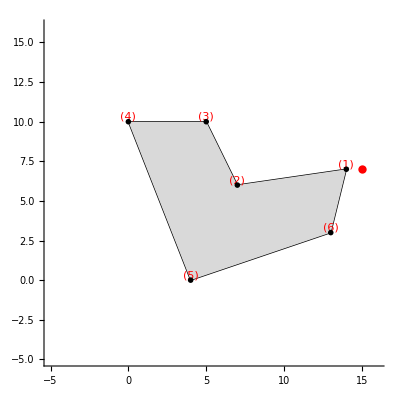

False

```mathematica
(*отобразить точку и многоугольник*)
point = {15,7};
Graphics[{Line[Append[P,P⟦1⟧]],LightGray,Polygon[P],{P/.{x_,y_}:>Text[Style[Position[P,{x,y}],Red],{x,y},{0,-1}]},Black,PointSize[.01], Point/@P,PointSize[0.015],Red,Point[point]}, PlotRange->{{-5,16},{-5,16}},Axes->True,AspectRatio->Automatic]
isInnerPoint[P,point]
```